```mathematica
NIntegrate[x^(-7/6)/(6*√(2* Pi * a^2))Exp[(-(x^(-1/6)-1)^2)/(2 a^2)]/.a->0.1,{x,0.001,Infinity}]
```

1.

```mathematica
P[x_,a_]:=x^(-7/6)/(6*√(2* Pi * a^2))Exp[(-(x^(-1/6)-1)^2)/(2 a^2)]
```

```mathematica
functionlist= Table[P[x,0.1*i],{i,1,3}];
line1 =Line[ {{1,0},{1,3}}];
```

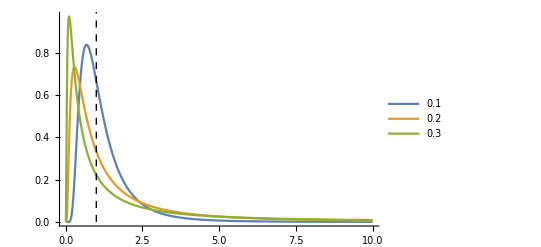

```mathematica
Plot[functionlist,{x,0.001,10},PlotRange->All,PlotLegends->{"0.1","0.2","0.3"},Epilog->{Directive[Dashed],line1}]
```

```mathematica
14+34
```

48